# AD for Sum of Squares

Many of the test functions are of the simple form
	f[x]=∑_(i=1)^(n-r) g(x[i:i+r]).
Functions like this are simple to differentiate.

For instance, the Rosenbrock function has r=1 and and
	g[{η_1,η_2}]=100(η_2-η_1^2)^2+(1-η_1)^2

```mathematica
TableForm[D[100.0 (η2-η1^2)^2+(1.0-η1)^2,{{η1,η2},2}]]
```

2+800. η1^2-400. (-η1^2+η2) | -400. η1
-400. η1 | 200.

```mathematica
PolynomialForms
```

PolynomialForms

```mathematica
Rosen[x_]:=Module[{sum=0.0,n=Length[x]},
Do[
sum+=100.0 (x⟦i+1⟧-x⟦i⟧^2)^2+(1.0-x⟦i⟧)^2,
{i,1,n-1}];
sum]
```

```mathematica
g[{η1_,η2_}]:= 100.0 (η2-η1^2)^2+(1.0-η1)^2
gradg[{η1_,η2_}]:= {-2 (1.0-η1)-400.0 η1 (-η1^2+η2),200.0 (-η1^2+η2)}
grad2g[{η1_,η2_}]:= {-2 (1.0-η1)-400.0 η1 (-η1^2+η2),200.0 (-η1^2+η2)}
f[g_,r_][x_]:=Module[{sum=0.0,n=Length[x]},
Do[
sum+=g[x⟦i;;i+r⟧],
{i,1,n-r}];
sum]

df[{g_,dg_},r_][x_,dx_]:=Module[{sum=0.0,n=Length[x],dsum=0.0},
dsum=0.0;
Do[
dsum+=dg[x⟦i;;i+r⟧].dx⟦i;;i+r⟧;
sum+=g[x⟦i;;i+r⟧],
{i,1,n-r}];
{sum,dsum}]

bf1[{g_,dg_},r_][x_]:=Module[
{sum=0.0,n=Length[x],grad=0.0 x},
Do[
grad⟦i;;i+r⟧+=dg[x⟦i;;i+r⟧];
sum+=g[x⟦i;;i+r⟧],
{i,1,n-r}];
{sum,grad}]

bf2[{g_,dg_},r_][x_]:=Module[
{sum=0.0,n=Length[x],grad=0.0 x},
Do[
sum+=g[x⟦i;;i+r⟧],
{i,1,n-r}];
Do[
grad⟦i;;i+r⟧+=dg[x⟦i;;i+r⟧];,
{i,n-r,1,-1}];
{sum,grad}]
```

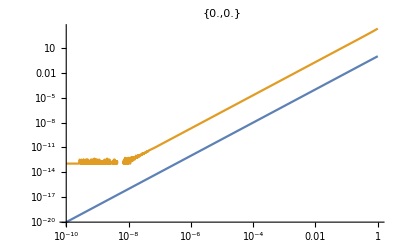

```mathematica
n=23;r=1;
{x0,dx0}=RandomReal[{-1,1},{2,n}];
{f0, df0}=df[{g,gradg},r][x0,dx0];
{f0, gradf1}=bf1[{g,gradg},1][x0];
{f0, gradf2}=bf2[{g,gradg},1][x0];
LogLogPlot[ {α^2,Abs[f0+α df0-f[g,r][x0+ α dx0]]},{α,10^-10,1},
PlotLabel->{gradf1.dx0-df0,Norm[gradf1-gradf2]}]
```

```mathematica
?Count
```

```mathematica
?Tally
```

{51,0,49}

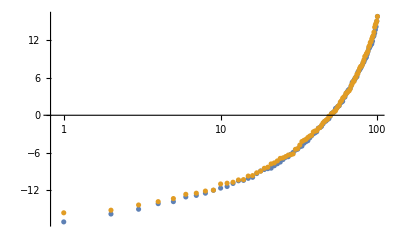

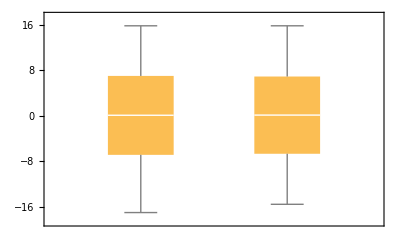

```mathematica
n=100;
A1=RandomReal[{-1,1},{n,n}];A1=A1+A1ᵀ;
λ1=Sort[Eigenvalues[A1]];
A2=RandomReal[{-1,1},{n,n}];A2=A2+A2ᵀ;
λ2=Sort[Eigenvalues[A2]];
(* Compute Index *)
Map[Count[Sign[λ],#]&,{-1,0,1}]
ListLogLinearPlot[{λ1,λ2}]
Histogram[λ1];
BoxWhiskerChart[{λ1,λ2},"Outliers"]
```

```mathematica
?BoxWhiskerChart
```